```mathematica
dim=8;
Clear[μ,η]
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
```

```mathematica
(* Set up Initial values(SIC),Initial Step, RG steps, W, Z1, LnZ1, DLnZ1, and constants*)
Clear[μ,η]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
```

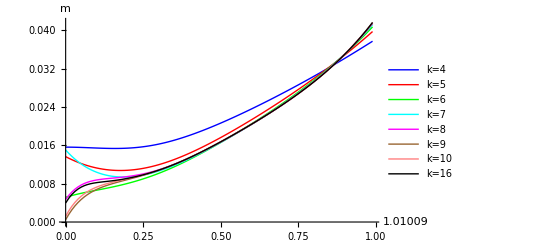

```mathematica
(***** Constants for magnetization: <m> vs μ; H=0.01 *****)
Clear[μ,η];
InitRGW;
μimin=0.00001;
μimax=1.0;
μiinc=0.01;
μiVector=Range[μimin,μimax,μiinc];
μVector=1.0/μiVector;
kVector={4,5,6,7,8,9,10,16};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-2*0.01];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=4","k=5","k=6","k=7","k=8","k=9","k=10","k=16"},PlotStyle->{Blue,Red,Green,Cyan, Magenta,Brown,Pink,Black},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

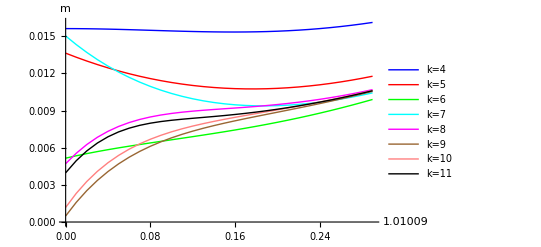

```mathematica
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]*0.3}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=4","k=5","k=6","k=7","k=8","k=9","k=10","k=11"},PlotStyle->{{Blue, Thick},{Red, Thick},{Green, Thick},{Cyan, Thick}, {Magenta, Thick},{Brown, Thick},{Pink, Thick},{Black, Thick}},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

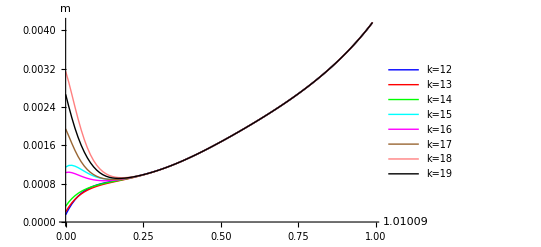

```mathematica
(***** Constants for magnetization: <m> vs μ; H=0.001 *****)
Clear[μ,η];
InitRGW;
μimin=0.00001;
μimax=1.0;
μiinc=0.01;
μiVector=Range[μimin,μimax,μiinc];
μVector=1.0/μiVector;
kVector={12,13,14,15,16,17,18,19};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-2*0.001];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=12","k=13","k=14","k=15","k=16","k=17","k=18","k=19"},PlotStyle->{Blue,Red,Green,Cyan, Magenta,Brown,Pink,Black},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

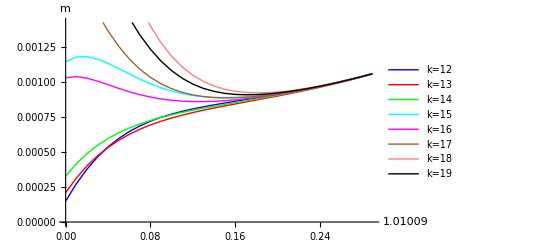

```mathematica
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]*0.3}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=12","k=13","k=14","k=15","k=16","k=17","k=18","k=19"},PlotStyle->{{Blue, Thick},{Red, Thick},{Green, Thick},{Cyan, Thick}, {Magenta, Thick},{Brown, Thick},{Pink, Thick},{Black, Thick}},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

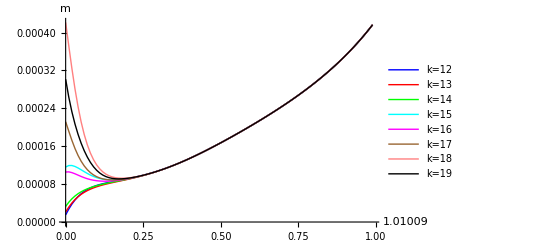

```mathematica
(***** Constants for magnetization: <m> vs μ; H=0.0001 *****)
Clear[μ,η];
InitRGW;
μimin=0.00001;
μimax=1.0;
μiinc=0.01;
μiVector=Range[μimin,μimax,μiinc];
μVector=1.0/μiVector;
kVector={12,13,14,15,16,17,18,19};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-2*0.0001];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=12","k=13","k=14","k=15","k=16","k=17","k=18","k=19"},PlotStyle->{Blue,Red,Green,Cyan, Magenta,Brown,Pink,Black},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

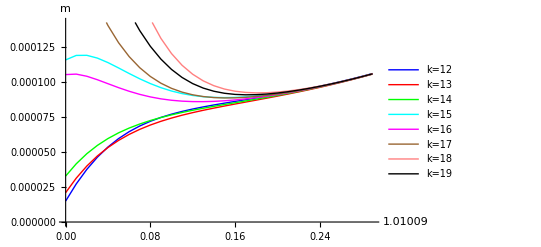

```mathematica
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]*0.3}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=12","k=13","k=14","k=15","k=16","k=17","k=18","k=19"},PlotStyle->{{Blue, Thick},{Red, Thick},{Green, Thick},{Cyan, Thick}, {Magenta, Thick},{Brown, Thick},{Pink, Thick},{Black, Thick}},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

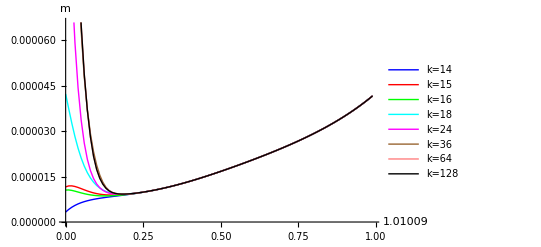

```mathematica
(***** Constants for magnetization: <m> vs μ; H=0.00001 *****)
Clear[μ,η];
InitRGW;
μimin=0.00001;
μimax=1.0;
μiinc=0.01;
μiVector=Range[μimin,μimax,μiinc];
μVector=1.0/μiVector;
kVector={14,15,16,18,24,36,64,128};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-2*0.00001];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=14","k=15","k=16","k=18","k=24","k=36","k=64","k=128"},PlotStyle->{Blue,Red,Green,Cyan, Magenta,Brown,Pink,Black},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

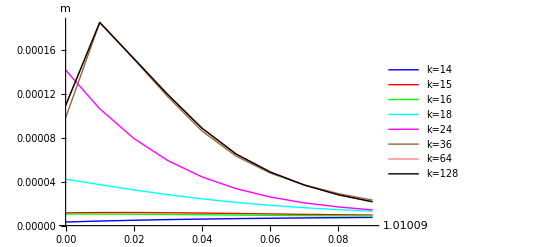

```mathematica
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]*0.1}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=14","k=15","k=16","k=18","k=24","k=36","k=64","k=128"},PlotStyle->{{Blue, Thick},{Red, Thick},{Green, Thick},{Cyan, Thick}, {Magenta, Thick},{Brown, Thick},{Pink, Thick},{Black, Thick}},AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->All]
```

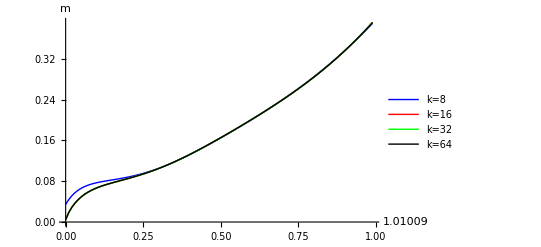

```mathematica
(***** Constants for magnetization: <m> vs μ; H0.1*****)
Clear[μ,η];
InitRGW;
μimin=0.00001;
μimax=1.0;
μiinc=0.01;
μiVector=Range[μimin,μimax,μiinc];
μVector=1.0/μiVector;
ηVector=Exp[-2*HVector];
kVector={8,16,32,64};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-2*0.1];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=16","k=32","k=64"},PlotStyle->{Blue,Red,Green,Black},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

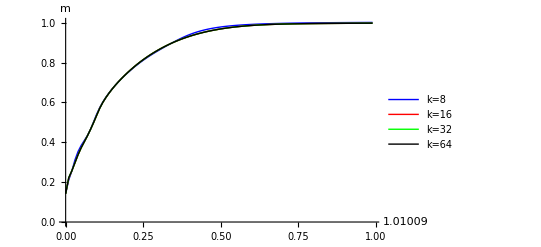

```mathematica
(***** Constants for magnetization: <m> vs μ; H1*****)
Clear[μ,η];
InitRGW;
μimin=0.00001;
μimax=1.0;
μiinc=0.01;
μiVector=Range[μimin,μimax,μiinc];
μVector=1.0/μiVector;
ηVector=Exp[-2*HVector];
kVector={8,16,32,64};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-2*1];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μiVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μiVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=16","k=32","k=64"},PlotStyle->{Blue,Red,Green,Black},AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

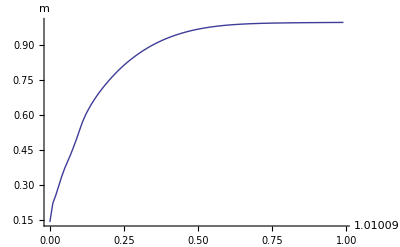

```mathematica
ListLinePlot[Table[{μiVector[[i]],Magμ[[4]][[i]]},{i,1,Dimensions[μiVector][[1]]}],AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->All]
```